# Centrifuge problem

## Find roots

### Hand-made function

```mathematica
MyFindRoots[z_,n_]:=Module[{roots,r,angle},
roots=ConstantArray[0,n];
For[k=0,k<n,k++,{
r:=Abs[z],
angle:=Arg[z],
r=r^(1/n),
roots[[k+1]]=r*Exp[I*(angle+2*Pi*k)/n]
}];
roots
]
```

### Native-based function

```mathematica
MyFindRootsNative[z_,n_]:=Solve[x^n==z,x][[All,1,2]]
```

### Summary

```mathematica
AbsoluteTiming[MyFindRoots[1+i,100000];]
AbsoluteTiming[MyFindRoots[1,100000];]
```

{1.87941,Null}

{1.30735,Null}

```mathematica
AbsoluteTiming[MyFindRootsNative[1+i,100000];]
AbsoluteTiming[MyFindRootsNative[1,100000];]
```

{3.27771,Null}

{0.655435,Null}

For arbitrary complex numbers, my hand-made method seems to be slightly faster, as it goes straight to business. I guess the Solve[] function is slower because it probably uses a different method to mine to solve this (which is quite algorithmic).

However, for our problem, which is “rotating” a number (1) on the complex plane, the native method using Solve[] destroys my method by taking half the time.

## Solver functions

### Reorder solutions clockwise

```mathematica
ReorderSet[set_]:=Module[{angles,order},
angles=Map[Arg,set];
order=Ordering[angles,All, NumericalOrder];
angles=angles[[order]];
Map[Exp,I*π *Rationalize[N[angles]/π]]
]
```

This step is probably the most important one to minimize calculations. Given the

### Solution finder

```mathematica
FindCentrifugeSols[n_]:=Module[{solutions,roots,subsets,subset,total, epsilon},
roots=MyFindRoots[1,n];
subsets:=Subsets[roots,n];
epsilon=Power[10,-15];
solutions={};
(*Main loop*)
For[i=1,i≤Length[subsets],i++,{
subset=subsets[[i]],
total=Total[subset],
If[Abs[N[total]] < epsilon,
solutions=Append[solutions,ReorderSet[subset]]
]
}];
(*Return*)
{roots,solutions}
]
```

### Rotation function

```mathematica
RotateSol[n_,k_,sol_]:=sol*Exp[I*(2*Pi*k)/n]
```

```mathematica
MakePositive[z_]:=Abs[z]*Exp[I*Arg[z]]
```

### Classify solutions by size

```mathematica
ClassifyCentrifugeSols[n_]:=Module[{MyMat,MyVect,roots,subsets,subset,epsilon,solutions},
solutions=FindCentrifugeSols[n];
subsets:=Sort[solutions[[2]]];
roots=solutions[[1]];
epsilon=Power[10,-15];
MyMat={};
MyVect={};
(*Main loop*)
For[i=1,i≤Length[subsets],i++,{
subset=subsets[[i]],
curr=Length[subset];
(*Check length of next element*)
If[i+1<=Length[subsets],
next=Length[subsets[[i+1]]],
next=0
];
(*Append subset to vector*)
MyVect=Append[MyVect,ReorderSet[subset]];
(*Append subsets to matrix*)
If[next!=Length[subset] && Length[MyVect]>0,
MyMat=Append[MyMat,{curr,MyVect}];
MyVect={};
];
}];
(*Return*)
{roots,MyMat}
]
```

### Reduce solutions

```mathematica
ReduceCentrifugeSols[n_]:=Module[{Sols,SubSols,UniqueSubSols,UniqueSols,MyLength,permuteSolsBool,RotatedSol,RotatedSols,Sol,Add},
Sols=ClassifyCentrifugeSols[n];
MyLength=Length[Sols[[2]]];
UniqueSols={};
(*Iterate over each subset size*)
For[i=1,i≤MyLength,i++,
UniqueSubSols={};
SubSols=Sols[[2]][[i]][[2]];
(*Loop over solution sub-space*)
For[element=1,element≤Length[SubSols],element++,
RotatedSols={};
Sol=SubSols[[element]];
Sol=ReorderSet[Sol];
(*Rotate one solution*)
For[k=0,k<n,k++,
RotatedSol=Map[MakePositive,RotateSol[n,k,Sol]];
RotatedSol=ReorderSet[RotatedSol];
RotatedSols=Append[RotatedSols,RotatedSol]
];
(*Add to list of unique solutions*)
If[Length[Intersection[UniqueSubSols,RotatedSols]]==0,
UniqueSubSols=Append[UniqueSubSols,Sol];
]
];
UniqueSols=Append[UniqueSols,{Sols[[2]][[i]][[1]],UniqueSubSols}];
];
(*Return*)
{Sols[[1]],UniqueSols}
]
```

## Drawing functions

### Plot complex solutions

```mathematica
PlotComplex[z_]:=ListPlot[
{Re[#],Im[#]}&/@z,
AxesOrigin->{0,0},
Axes->False,
PlotRange->{{-1.2,1.2},{-1.2,1.2}},
ImagePadding->0,
AspectRatio->1,
Frame->False,
FrameLabel->{{Im,None},{Re,None}},
PlotStyle->Directive[Red,PointSize[.2]]
]
```

```mathematica
PlotComplexBase[z_]:=ListPlot[
{Re[#],Im[#]}&/@z,
AxesOrigin->{0,0},
Axes->False,
PlotRange->{{-1.2,1.2},{-1.2,1.2}},
ImagePadding->0,
AspectRatio->1,
Frame->False,
FrameLabel->{{Im,None},{Re,None}},
PlotStyle->Directive[GrayLevel[0.7],PointSize[0.2]]
]
```

```mathematica
PlotFullCentrif[z_,roots_]:=Show[
Graphics@Circle[{0,0},1],
PlotComplexBase[roots],
PlotComplex[z],
ImageSize->Tiny]
```

### Draw all solutions

```mathematica
DrawCentrifugeSols[n_]:=Module[{MyMat,MyVect,roots,subsets,subset,epsilon,solutions},
solutions=FindCentrifugeSols[n];
subsets:=Sort[solutions[[2]]];
roots=solutions[[1]];
epsilon=Power[10,-15];
MyMat={{"Elements","Representation"}};
MyVect={};
(*Main loop*)
For[i=1,i≤Length[subsets],i++,{
subset=subsets[[i]],
curr=Length[subset];
(*Check length of next element*)
If[i+1<=Length[subsets],
next=Length[subsets[[i+1]]],
next=0
];
(*Create plots*)
MyVect=Append[
MyVect,
Show[Graphics@Circle[{0,0},1],PlotComplexBase[roots],PlotComplex[subset],ImageSize->Tiny]
];
(*Append plots to matrix*)
If[next!=Length[subset] && Length[MyVect]>0,
MyMat=Append[MyMat,{curr,MyVect}];
MyVect={};
];
}];
Print["Roots for ",n, " holes: ",roots];
Print["Solutions:"];
(*Return*)
Grid[MyMat,
Background->{None,{Lighter[Yellow,.9],None}},
Alignment->{{Center,Left}}, 
Dividers->{All,All}
]
]
```

### Draw unique solutions

```mathematica
DrawCentrifugeUniqueSols[n_]:=Module[{NumSubSets,roots,solutions,MyMat},
solutions=ReduceCentrifugeSols[n];
roots=solutions[[1]];
NumSubSets=Length[solutions[[2]]];
MyMat={{"Elements","Representation"}};
(*Loop over subsets*)
For[i=1,i≤NumSubSets,i++,
MyMat=Append[
MyMat,
{solutions[[2]][[i]][[1]],
PlotFullCentrif[#,roots]&/@solutions[[2]][[i]][[2]]}
]
];
Print["Roots for ",n, " holes: ",roots];
Print["Solutions:"];
(*Return*)
Grid[MyMat,
Background->{None,{Lighter[Yellow,.9],None}},
Alignment->{{Center,Left}}, 
Dividers->{All,All}
]
]
```

## Solutions and examples

### All solutions

```mathematica
AbsoluteTiming[FindCentrifugeSols[6]]
```

{0.007257,{{1,ⅇ^((ⅈ π)/3),ⅇ^((2 ⅈ π)/3),-1,ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/3)},{{},{1,-1},{ⅇ^(-(2 ⅈ π)/3),ⅇ^((ⅈ π)/3)},{ⅇ^(-(ⅈ π)/3),ⅇ^((2 ⅈ π)/3)},{ⅇ^(-(2 ⅈ π)/3),1,ⅇ^((2 ⅈ π)/3)},{ⅇ^(-(ⅈ π)/3),ⅇ^((ⅈ π)/3),-1},{ⅇ^(-(2 ⅈ π)/3),1,ⅇ^((ⅈ π)/3),-1},{ⅇ^(-(ⅈ π)/3),1,ⅇ^((2 ⅈ π)/3),-1},{ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/3),ⅇ^((ⅈ π)/3),ⅇ^((2 ⅈ π)/3)},{ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/3),1,ⅇ^((ⅈ π)/3),ⅇ^((2 ⅈ π)/3),-1}}}}

Roots for 12 holes: {1,ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅈ,ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1,ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6)}

Solutions:

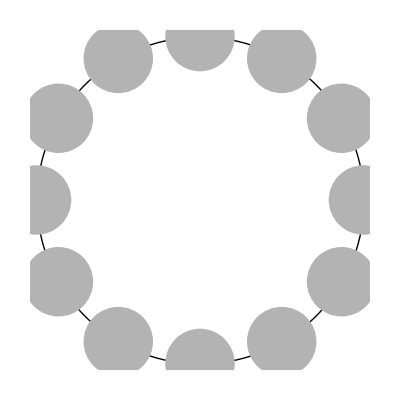
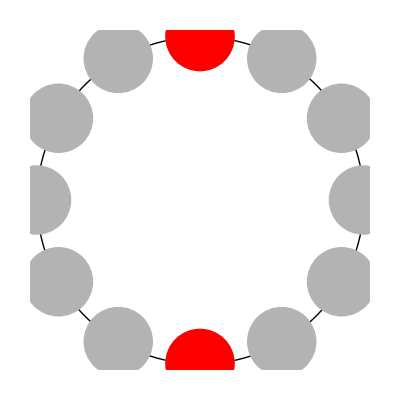
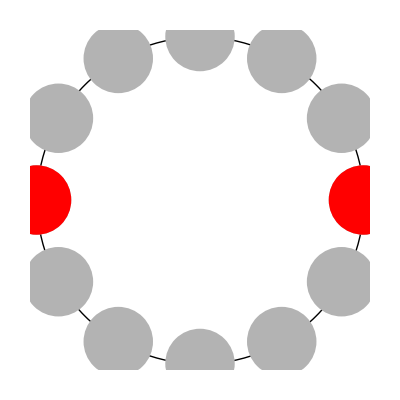
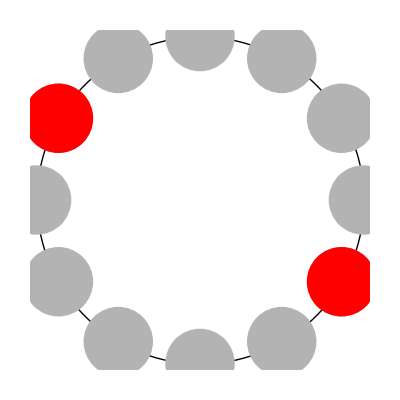
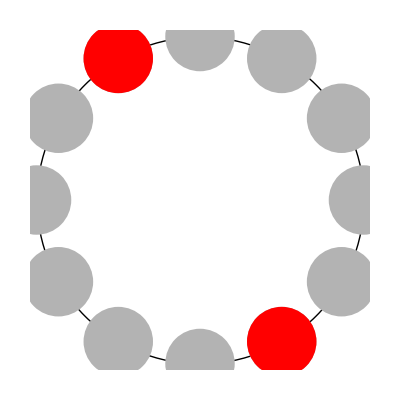
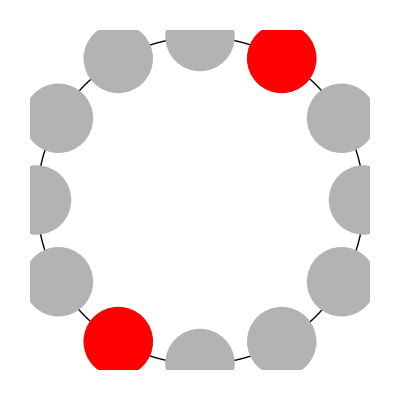
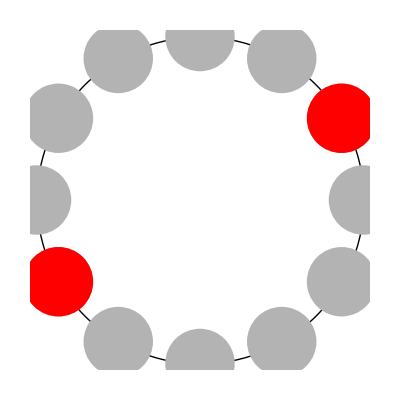
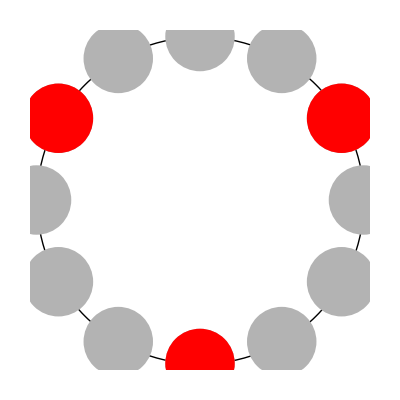
{16.5964,Elements | Representation
0 | {-Graphics-}
2 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
3 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-}
4 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
5 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
6 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
7 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
8 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
9 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-}
10 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
12 | {-Graphics-}}

```mathematica
AbsoluteTiming[DrawCentrifugeSols[12]]
```

### Unique solutions

```mathematica
AbsoluteTiming[SolsSix=ReduceCentrifugeSols[6]]
```

{0.052211,{{1,ⅇ^((ⅈ π)/3),ⅇ^((2 ⅈ π)/3),-1,ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/3)},{{0,{{}}},{2,{{1,-1}}},{3,{{ⅇ^(-(ⅈ π)/3),ⅇ^((ⅈ π)/3),-1}}},{4,{{ⅇ^(-(ⅈ π)/3),1,ⅇ^((2 ⅈ π)/3),-1}}},{6,{{ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/3),1,ⅇ^((ⅈ π)/3),ⅇ^((2 ⅈ π)/3),-1}}}}}}

```mathematica
Grid[SolsSix[[2]]]
```

0 | {{}}
2 | {{1,-1}}
3 | {{ⅇ^(-(ⅈ π)/3),ⅇ^((ⅈ π)/3),-1}}
4 | {{ⅇ^(-(ⅈ π)/3),1,ⅇ^((2 ⅈ π)/3),-1}}
6 | {{ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/3),1,ⅇ^((ⅈ π)/3),ⅇ^((2 ⅈ π)/3),-1}}

```mathematica
AbsoluteTiming[DrawCentrifugeUniqueSols[12]]
```

{19.4672,Elements | Representation
0 | {-Graphics-}
2 | {-Graphics-}
3 | {-Graphics-}
4 | {-Graphics-,-Graphics-,-Graphics-}
5 | {-Graphics-}
6 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
7 | {-Graphics-}
8 | {-Graphics-,-Graphics-,-Graphics-}
9 | {-Graphics-}
10 | {-Graphics-}
12 | {-Graphics-}}

### Examples for the blog

Roots for 8 holes: {1,ⅇ^((ⅈ π)/4),ⅈ,ⅇ^((3 ⅈ π)/4),-1,ⅇ^(-(3 ⅈ π)/4),-ⅈ,ⅇ^(-(ⅈ π)/4)}

Solutions:

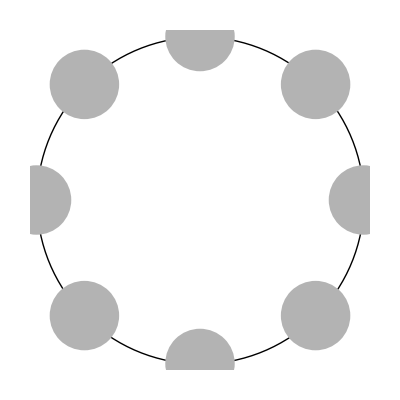
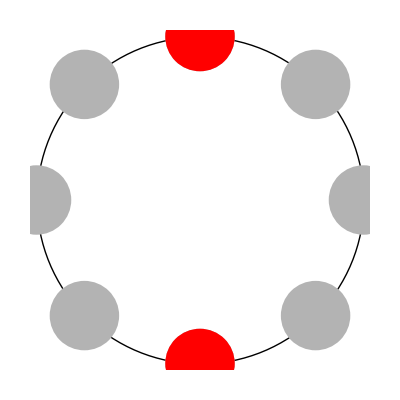
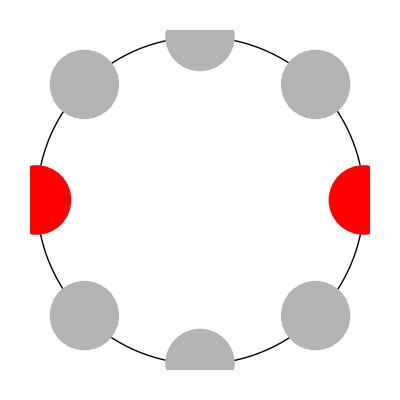
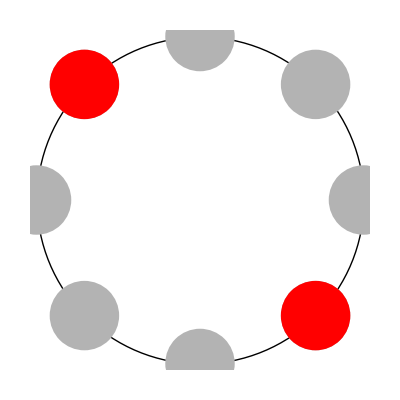
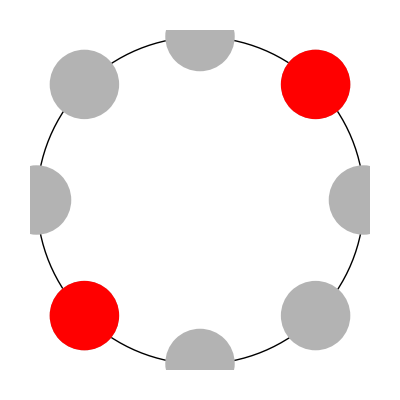
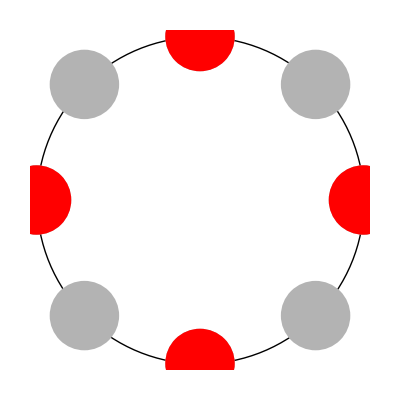
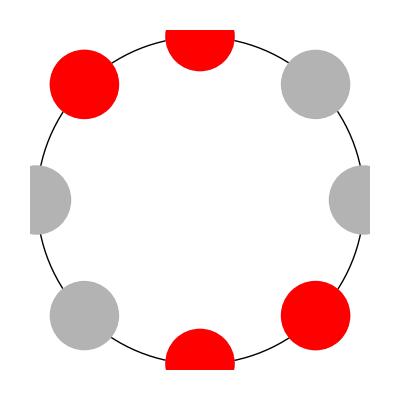
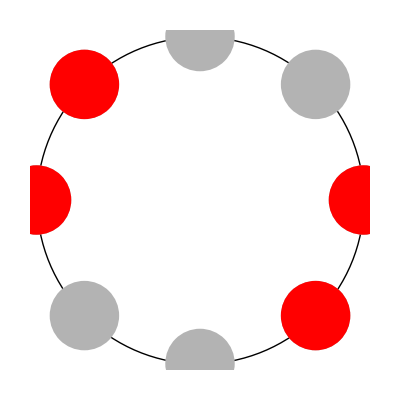
Elements | Representation
0 | {-Graphics-}
2 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-}
4 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
6 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-}
8 | {-Graphics-}

```mathematica
DrawCentrifugeSols[8]
```

```mathematica
DrawCentrifugeUniqueSols[8]
```

Roots for 8 holes: {1,ⅇ^((ⅈ π)/4),ⅈ,ⅇ^((3 ⅈ π)/4),-1,ⅇ^(-(3 ⅈ π)/4),-ⅈ,ⅇ^(-(ⅈ π)/4)}

Solutions:

Elements | Representation
0 | {-Graphics-}
2 | {-Graphics-}
4 | {-Graphics-,-Graphics-}
6 | {-Graphics-}
8 | {-Graphics-}